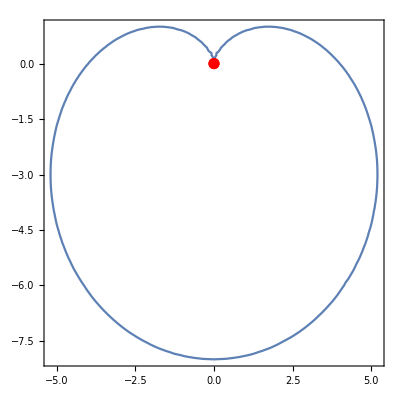

```mathematica
(* (x^2 + y^2 + 4y)^2 - 16(x^2 + y^2) = 0 *)
curve1=ContourPlot[(x^2+y^2+4y)^2-16(x^2+y^2)==0,{x,-10,10},{y,-10,6}];
singularPoints1=NSolve[{(x^2+y^2+4y)^2-16(x^2+y^2)==0,D[(x^2+y^2+4y)^2-16(x^2+y^2),x]==0,D[(x^2+y^2+4y)^2-16(x^2+y^2),y]==0},{x,y}];
Show[curve1,Graphics[{Red,PointSize[0.02],Point[{x,y}]/.singularPoints1}],PlotRange->All]
```

```mathematica
singularPoints1
```

{{x→0.,y→0.},{x→0.,y→0.}}

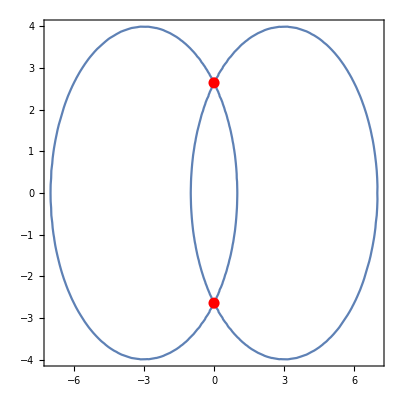

```mathematica
(* 2(x^2 + 9)(y^2 − 16) + (x^2 − 9)^2 + (y^2 − 16)^2 = 0 *)
curve2=ContourPlot[2(x^2+9)(y^2-16)+(x^2-9)^2+(y^2-16)^2==0,{x,-10,10},{y,-10,10}];
singularPoints2=NSolve[{2(x^2+9)(y^2-16)+(x^2-9)^2+(y^2-16)^2==0,D[2(x^2+9)(y^2-16)+(x^2-9)^2+(y^2-16)^2,x]==0,D[2(x^2+9)(y^2-16)+(x^2-9)^2+(y^2-16)^2,y]==0},{x,y}];
Show[curve2,Graphics[{Red,PointSize[0.02],Point[{x,y}]/.singularPoints2}],PlotRange->All]
```

```mathematica
singularPoints2
```

{{x→0.,y→2.64575},{x→0.,y→-2.64575}}

```mathematica
(* 350(x^2)(y^2) − (15^2)(x^2 + y^2) + (12^2)(x^4 + y^4) + 81 = 0 *)
curve3=ContourPlot[350(x^2)(y^2)−(15^2)(x^2+y^2)+(12^2)(x^4+y^4)+81==0,{x,-5,5},{y,-5,5}];
singularPoints3=NSolve[{350(x^2)(y^2)−(15^2)(x^2+y^2)+(12^2)(x^4+y^4)+81==0,D[350(x^2)(y^2)−(15^2)(x^2+y^2)+(12^2)(x^4+y^4)+81,x]==0,D[350(x^2)(y^2)−(15^2)(x^2+y^2)+(12^2)(x^4+y^4)+81,y]==0},{x,y}];
Show[curve3,Graphics[{Red,PointSize[0.02],Point[{x,y}]/.singularPoints3}],PlotRange->All]
```

-Graphics-

```mathematica
singularPoints3
```

{}

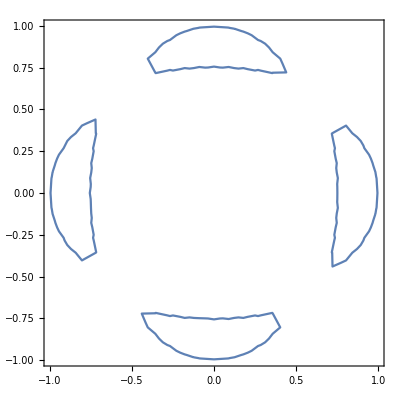

```mathematica
Show[curve3, PlotRange -> All]
```

```mathematica
Grad[81+350 x^2 y^2-225 (x^2+y^2)+144 (x^4+y^4),{x,y}]
```

{-450 x+576 x^3+700 x y^2,-450 y+700 x^2 y+576 y^3}